# Chapter 4 pt. 1: Energy efficient QND measurement and read-out

## Author: Bruno Ortega Goes

This code organized written by me ensembles in a organized manner my own codes and some codes produced by Stephen Wein, PhD. It produces the images presented in the paper arXiv:2205.09623 and in the thesis.

```mathematica
(*Setting the path where the plots are going to be saved.*)
nbdirectory=SetDirectory[NotebookDirectory[]];
plotsPath =nbdirectory<>"/PlotsChap4/";

Clear[savePlot];
savePlot[nameAndExtension_,plot_,path_:plotsPath]:=If[Length@path ==0,Export[path<>nameAndExtension,plot],  Do[
Export[PlotsPath<>nameAndExtension,plot],{PlotsPath,path}]]

fontsize = 24;
```

## Vectorization☑

```mathematica
(*Easy to call *)
Clear[eye,tp,kp];
eye = IdentityMatrix;
tp = Transpose;
kp = KroneckerProduct;
```

```mathematica
Clear[a,coherentState];
a[Nmax_]:=Transpose[Table[If[i==j+1,Sqrt[i-1],0],{i,1,Nmax},{j,1,Nmax}]];
coherentState[α_,Ν_]:=Table[Exp[-Abs[α]^2/2]*α^n/Sqrt[n!],{n,0,Ν}]/Sqrt[Sum[Exp[-Abs[α]^2]*Abs[α]^(2n)/(n!),{n,0,Ν}]];
```

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c,tp[c†]] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[H,ℐ]- kp[ℐ,tp[H]])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L, tp[L†]]-1/2 kp[(L†.L),ℐ]-1/2 kp[ℐ,tp[L†.L]]];
leftacting[A_]:=kp[A,eye[Length@A]];
```

Below is my way of doing the vectorization which used column stacking, it turned out to give different results from the ones Stephen has got

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c*,c] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[ℐ,H]- kp[Hᵀ,ℐ])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L*,L]-1/2 kp[tp[(L†.L)],ℐ]-1/2 kron[ℐ,L†.L]];
```

```mathematica
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
```

## Hilbert Space ☑

```mathematica
dim4LS = 4;
dimSource = 4;
dim = dim4LS dimSource^2;
(*Ordering the 4LS basis as:*)
{spinDw,spinUp,trionDw,trionUp} = {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Dipole operators*)
(*This is enough for the semiclassical model*)
ΣL = Outer[Times, spinDw,trionDw];
ΣR = Outer[Times, spinUp,trionUp];
ΣH = (ΣR+ΣL)/(√2);
ΣV = (ΣR-ΣL)/(ⅈ √2);
ΣD = (ΣH +ΣV)/(√2);
ΣA = (ΣH-ΣV)/(√2);
```

```mathematica
(*Dipole Operators in the large Hilbert Space*)
(*This is necessary for the SLH framework*)
σL = kp[ΣL, eye[dimSource], eye[dimSource]];
σR = kp[ΣR, eye[dimSource], eye[dimSource]];
```

```mathematica
(*Virtual cavity operators*)
𝕒R = kp[eye[dim4LS],a[dimSource],eye[dimSource]]//N;
𝕒L = kp[eye[dim4LS],eye[dimSource],a[dimSource]]//N;
```

## Pre-measurement: qBhat ☑

## Semiclassical drive ☑

Defining the physical system:

```mathematica
Hsemiclassical = ⅈ α (ΣH - ΣH†)//mf;
ℒsemiclassical = unitary2vec[Hsemiclassical]+ γ lindblad2vec[ΣL]+ γ lindblad2vec[ΣR]//Refine//mf;
dimSC = Length@Hsemiclassical;
traceSC = Flatten[eye[dimSC]];
```

(0 | 0 | (ⅈ α)/(√2) | 0
0 | 0 | 0 | (ⅈ α)/(√2)
-(ⅈ α)/(√2) | 0 | 0 | 0
0 | -(ⅈ α)/(√2) | 0 | 0)

(0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0 | 0
-α/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0
0 | -α/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0 | γ
0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α/(√2) | 0
0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α/(√2)
-α/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | α/(√2) | 0 | 0 | 0 | 0 | 0
0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | α/(√2) | 0 | 0 | 0 | 0
0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | α/(√2) | 0
0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | α/(√2)
0 | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | 0 | 0 | 0 | 0 | -α/(√2) | 0 | -γ)

Initial state and qBhat computer:

```mathematica
ψ04LS=(spinUp+spinDw)/(√2);
vecρ04LS = Flatten[kp[ψ04LS,ψ04LS]];
```

```mathematica
σupdw = Outer[Times,spinDw,spinUp]//mf;
σupdw =leftacting[σupdw] //mf;
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Finding the steady state qBhat, ℬqcsSS (this is an efficient method based on Dr. Wein’s code):

```mathematica
ℬqcsSS=Limit[(traceSC.σupdw.MatrixExp[ℒsemiclassical t/.α->0].MatrixExp[ℒsemiclassical τ,vecρ04LS])/.γ->1/.τ->1/Γ/.α->√(nH Γ),t->∞]
```

1/(4 (1-8 nH Γ))ⅇ^(-1/2/Γ) (ⅇ^(1/(2 Γ)+(-1-√(1-8 nH Γ))/(2 Γ))+ⅇ^(1/(2 Γ)+(-1+√(1-8 nH Γ))/(2 Γ))-8 nH Γ-4 ⅇ^(1/(2 Γ)+(-1-√(1-8 nH Γ))/(2 Γ)) nH Γ-4 ⅇ^(1/(2 Γ)+(-1+√(1-8 nH Γ))/(2 Γ)) nH Γ-ⅇ^(1/(2 Γ)+(-1-√(1-8 nH Γ))/(2 Γ)) √(1-8 nH Γ)+ⅇ^(1/(2 Γ)+(-1+√(1-8 nH Γ))/(2 Γ)) √(1-8 nH Γ))

Here there is a 3.8 re-scaling of the Γ.

```mathematica
coherentsetsemiclassical=N@ParallelTable[{10^x,10^y/3.8,Chop[ℬqcsSS/.{nH->10^x,Γ->10^y/3.8}]},{x,-1,2,2 10^-2},{y,-2,2,2 10^-2}];(*The Γ is re-scaled by a factor 3.8*)
```

```mathematica
coherentsetsemiclassical=Flatten[coherentsetsemiclassical,1]
```

{{0.1,0.00263158,0.409754},{0.1,0.0027556,0.409772},30348,{100.,26.3158,0.0192338}}
 |  |  |  |

First look at the plot:

```mathematica
ListContourPlot[coherentsetsemiclassical,ScalingFunctions->{"Log","Log"}]
```

-Graphics-

Making it stylish:

```mathematica
(*Define a custom color function*)colorf=ColorData[{"TemperatureMap","Reverse"}][Rescale[#,{0,1}]]&;

Fig1=ListContourPlot[coherentsetsemiclassical,
AspectRatio->10/15,
ImageSize->500,
ScalingFunctions->{"Log","Log"},
ColorFunction->colorf,
ColorFunctionScaling->True,FrameLabel->{Style["Average photon number, n_H",22,Black],Style["Pulse bandwith, Γ/γ",22,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->22,Black],PlotLegends->Placed[BarLegend[{ColorData[{"TemperatureMap","Reverse"}],{0,1}},LegendLabel->Style["ℬ_q^cs",22,Black]],Right],
FrameTicksStyle->Directive[FontSize->18,Black]]

savePlot["qBhatCoherent.pdf", Fig1];

(*Export[overleafPathchap4<>"Fig1.png",Fig1];
Export[overleafPathchap4<>"Fig1.pdf",Fig1];
Export[overleafPathchap4<>"Fig1.svg",Fig1];*)
```

-Graphics-

Cutting out the low energy sector:

```mathematica
lowenergysector = {{All,1},{All,10}};

plotlow=ListContourPlot[coherentsetsemiclassical,
PlotRange->lowenergysector,
ScalingFunctions->{"Log","Log"},
ColorFunction->colorf,
ColorFunctionScaling->True,(*Disable color function scaling*)FrameLabel->{Style["Average photon number, (n̄)_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->22,Black],PlotLegends->Placed[BarLegend[{ColorData[{"TemperatureMap","Reverse"}],{0,1}},LegendLabel->Style["ℬ_q^cs",22,Black]],Right],
Epilog->Inset[Style["(a)",22,White],Scaled[{0.05,0.95}],{Left,Top}],
FrameTicksStyle->Directive[FontSize->18,Black],
AspectRatio->3/2,
ImageSize->350]
savePlot["LowEnergyqBhatCoherent.pdf", %];
```

-Graphics-

Defining and plotting the qBhat for the quantum state, ℬqqs:
This is the analytical expression obtained from the model.

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];

quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
ColorFunctionScaling->False,
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Single photon probability, p_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Black],PlotLegends->Placed[BarLegend[{ColorData[{"TemperatureMap","Reverse"}],{0,1}},LegendLabel->Style["ℬ_q^qs",22,Black]],Right],
Epilog->Inset[Style["(b)",22,White],Scaled[{0.05,0.95}],{Left,Top}],
AspectRatio->3/2,
ImageSize->350];
(*The line where the plot is zero.*)
zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];
(*Show the contour plot and the zero line*)
qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
(*savePlot["qBhatLowEnergyComparisonPresentation.jpg",%];*)
```

-Graphics-

Show the comparison of the qBhat for the coherent and quantum state:

```mathematica
Fig2=Grid[{{plotlow,qBhatqsPlot}}]
savePlot["qBhatLowEnergyComparison.pdf",%]
savePlot["qBhatLowEnergyComparison.jpg",%%]
```

-Graphics- | -Graphics-

/Users/brunogoes/Dropbox/GitHub/ThesisSPI/Chapter4/PlotsChap4/qBhatLowEnergyComparison.pdf

/Users/brunogoes/Dropbox/GitHub/ThesisSPI/Chapter4/PlotsChap4/qBhatLowEnergyComparison.jpg

## Spin read-out:cBhat

## Protocol definition

```mathematica
<<cascadedLiouvillian.mx
```

The experiment must be modelled step-by-step. This part of the code was organized by me and is based on the original code written by Dr. Wein. It models the experiment and uses the method presented in Ref. https://arxiv.org/pdf/2004.04786.pdf .
1) The pulse with one photon passes through the beam splitter:

```mathematica
uL = Cos[θ1]𝕒L;
uR = Cos[θ1]𝕒R;
dL = ⅈ Sin[θ1] 𝕒L;
dR = ⅈ Sin[θ1] 𝕒R;
```

2) Part of the pulse will interact with the SPI, hence the Hamiltonian of the light-matter interaction is:

```mathematica
h0 =ΔL σL†.σL +ΔR σR†.σR;
hSPI = -ⅈ (√ηlm √(γ η κ))/2((σL†.uL-uL†.σL)+(σR†.uR-uR†.σR));
```

Cascaded coupling Hamiltonian assumes the form:

```mathematica
hcas = h0 + hSPI;
```

3) We write the output modes “u” and “d”:

```mathematica
Loutu = √ηd(√γ σL + √(η κ)uL);
Routu = √ηd(√γ σR + √(η κ)uR);

Loutd = √ηd √(η κ)dL;
Routd = √ηd √(η κ)dR;
```

4) Passing through the BS again:

```mathematica
RoutD1 = Cos[θ2]Routu + ⅈ Exp[ⅈ ϕ]Sin[θ2] Routd ;
LoutD1 = Cos[θ2]Loutu + ⅈ Exp[ⅈ ϕ]Sin[θ2] Loutd ;

RoutD2 = Exp[ⅈ ϕ] Cos[θ2] Routd + ⅈ Sin[θ2]Routu;
LoutD2 = Exp[ⅈ ϕ]Cos[θ2]Loutd+ⅈ Sin[θ2]Loutu;
```

5) Defining the (vectorized) Liouvillian:

```mathematica
(*Coherent part*)
PrettyTiming[
ℋ = unitary2vec[hcas];
(*Virtual cavity and 4LS decay*)
𝒟γ=lindblad2vec[Loutu] + lindblad2vec[Routu]+lindblad2vec[Loutd]+lindblad2vec[Routd]+(1-η)κ(lindblad2vec[𝕒R]+lindblad2vec[𝕒L]);
(*Decay with correlation due to cascaded coupling*)
𝒟γs = γs lindblad2vec[σL†.σL]+γs lindblad2vec[σR†.σR]+κs lindblad2vec[𝕒L†.𝕒L]+κs lindblad2vec[𝕒R†.𝕒R];

(*Conditional evolution*)
𝒟ηd = -ηRD1 jump[RoutD1]-ηRD2 jump[RoutD2]-ηLD1 jump[LoutD1]-ηLD2 jump[LoutD2];
]
```

0h : 2m : 56s

Total system Liouvillian:

```mathematica
PrettyTiming[ℒcas = ℋ + 𝒟γ+𝒟γs+𝒟ηd;]
```

0h : 0m : 7s

```mathematica
(*Checking dimensions and type of the Liouvillian*)
Dimensions@ℒcas
Head@ℒcas
```

{4096,4096}

List

This takes some time to be built, so let’s save this guy:

```mathematica
DumpSave["cascadedLiouvillian.mx",ℒcas]
```

{{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4085,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},4094,{1}}}
 |  |  |  |

Since the dimension is huge we want to check what are the states that will be explored during the dynamics. To do so, we make an exploration of the fock-Liouville space in what follows.

We put some dummy parameters to get information and use the information that we know the initial states of the field, R, and the 4LS.

## Fock-space exploration to dimension reduction

Choose a parameter set to explore the Fock-Liouville space:

```mathematica
par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->0.01,(* Decay rates *)
η->0.9,ηlm->0.9,ηd->0.9,(* Input/coupling efficiency *)
ηRD1->0.5,ηRD2->0.5,ηLD1->0.5,ηLD2->0.5,(* Detector efficiency/conditional evolution parameters *)
γs->0.1,κs->0.1,(* Dephasing *)
ϕ->0.235,(* interferometer phase *)
θ1->0.412,θ2->0.12(* Beam splitter ratios *)
};
```

Choose an initial state to reduce the necessary subspace: gs spin superposition + H-polarized input coherent state (up to 3 photons):

Is it a number?Did I forget to substitute some variable?

```mathematica
Chop@Total[Flatten[ℒcas/.par]]
```

-3023.86

Choose an initial state to reduce the necessary subspace: gs spin superposition + H-polarized input coherent state (up to 3 photons):

```mathematica
istate=Flatten[kp[{1,1,0,0},{1,1,1,1},{1,0,0,0}]];
istate=Flatten[kp[istate,istate]];
```

```mathematica
aux1 = Sign[istate]*Range[dim^2];(*Sign of initial state assigns 1 to positive values, 0 when the value is 0 and -1 when the value is negative. Range[Dim2] makes a big list going from 1 to 4096. The output is a list with a bunch of zeros and the indexes of the initial nodes where the values are not zero.*)
```

```mathematica
initialnodes=DeleteCases[aux1,0];(*every place where the value of aux 1 is zero are neglected*)
```

```mathematica
initialnodes
```

{1,5,9,13,17,21,25,29,257,261,265,269,273,277,281,285,513,517,521,525,529,533,537,541,769,773,777,781,785,789,793,797,1025,1029,1033,1037,1041,1045,1049,1053,1281,1285,1289,1293,1297,1301,1305,1309,1537,1541,1545,1549,1553,1557,1561,1565,1793,1797,1801,1805,1809,1813,1817,1821}

```mathematica
aux2= NumericQ/@Flatten[ℒcas+x*eye[Length[ℒcas]]]/.{True->0,False->1}
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16777136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
 |  |  |  |

```mathematica
Dimensions@aux2
Head@aux2
```

{16777216}

List

```mathematica
adjacencymatrix=Partition[aux2,dim^2];
```

```mathematica
Dimensions@adjacencymatrix
Head@adjacencymatrix
```

{4096,4096}

List

```mathematica
vertstyle=Table[i->If[MemberQ[initialnodes,Range[dim^2][[i]]],Red,Black],{i,dim^2}];
```

```mathematica
aux3=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

{1}
 |  |  |  |

```mathematica
Dimensions@aux3
Head@aux3
```

{4096,4096}

List

```mathematica
AdjacencyGraph[aux3,
VertexStyle->vertstyle,
PlotLabel->"Full Fock-Liouville space and intereactions for the ME",
Frame->True,
FrameLabel->{"Red dot is the initial state"}]
```

```mathematica
(* This applies the propagator once to see which Fock-Liouville states become populated *)
expState=Sign[Abs[MatrixExp[ℒcas/.par].istate]];
```

```mathematica
Dimensions@expState
Head@expState
```

{4096}

List

```mathematica
aux4=expState*Range[dim^2];(*Encontrando os indexes*)
```

```mathematica
(* Let's now look at all the Fock-Liouville basis vectors that were explored *)
nodeset=DeleteCases[aux4,0];
```

```mathematica
nodeset
```

{1,5,9,13,17,21,25,29,49,53,57,257,261,265,269,273,277,281,285,305,309,313,513,517,521,525,529,533,537,541,561,565,569,769,773,777,781,785,789,793,797,817,821,825,1025,1029,1033,1037,1041,1045,1049,1053,1073,1077,1081,1281,1285,1289,1293,1297,1301,1305,1309,1329,1333,1337,1537,1541,1545,1549,1553,1557,1561,1565,1585,1589,1593,1793,1797,1801,1805,1809,1813,1817,1821,1841,1845,1849,3073,3077,3081,3085,3089,3093,3097,3101,3121,3125,3129,3329,3333,3337,3341,3345,3349,3353,3357,3377,3381,3385,3585,3589,3593,3597,3601,3605,3609,3613,3633,3637,3641}

```mathematica
aux5=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

{1}
 |  |  |  |

```mathematica
aux6 = aux5[[nodeset,nodeset]]
```

{1}
 |  |  |  |

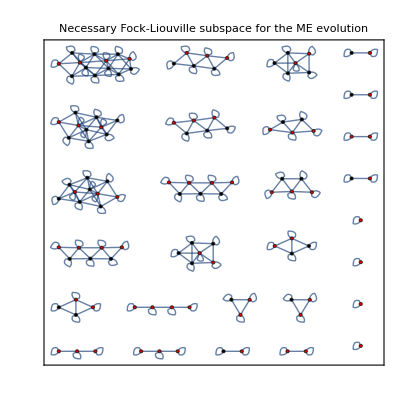

```mathematica
AdjacencyGraph[aux6,VertexStyle->Table[i->If[MemberQ[initialnodes,nodeset[[i]]],Red,Black],{i,Length[nodeset]}],PlotLabel->"Necessary Fock-Liouville subspace for the ME evolution",Frame->True,FrameLabel->{"Red dots are the initial state"}]
```

## cBhat simulation

Now that we know which states are accessed durign the dynamics we can restrict the analysis to this smaller subspace:

```mathematica
ℒSS = ℒcas[[nodeset,nodeset]];
initialstateSS = istate[[nodeset]];
traceSS = Flatten[eye[dim]][[nodeset]];
```

```mathematica
Head@ℒSS
Dimensions@ℒSS
Head@initialstateSS
Dimensions@initialstateSS
Head@traceSS
Dimensions@traceSS
```

List

{121,121}

List

{121}

List

{121}

```mathematica
(* Choose a parameter set to explore the Fock-Liouville space *)
outset=ParallelTable[
effN=1;
dephN=0;

par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->10^k,(* Decay rates *)
η->effN,ηlm->1,ηd->1,(* Input/coupling efficiency *)
ηRD1->0.,ηRD2->0.,ηLD1->0.,ηLD2->0.,(* Detector efficiency/conditional evolution parameters *)
γs->dephN,κs->0dephN,(* Dephasing *)
ϕ->0,(* interferometer phase *)
θ1->0,θ2->0
};

traceSS=Flatten[eye[dim]][[nodeset]];
σupdw = Outer[Times,spinDw,spinUp];
σupdw=kp[σupdw,eye[dimSource],eye[dimSource]];
σupdw=kp[σupdw,eye[dim]][[nodeset,nodeset]];

istate=Flatten[kp[{1,1,0,0}/√2,{1,1,0,0}/√2,{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
phtOut12=traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate;

istate=Flatten[kp[{1,1,0,0}/√2,{0,1,0,0},{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
phtOut=traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate;

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],coherentState[1/Sqrt[2],3],{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
cohOut12=traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate;

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],coherentState[1,3],{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
cohOut=traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate;

par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->10^k,(* Decay rates *)
η->effN,ηlm->1,ηd->1,(* Input/coupling efficiency *)
ηRD1->0.,ηRD2->0.,ηLD1->0.,ηLD2->0.,(* Detector efficiency/conditional evolution parameters *)
γs->dephN,κs->0dephN,(* Dephasing *)
ϕ->0,(* interferometer phase *)
θ1->π/4,θ2->π/4
};

tsplit=2;

Dset={ηRD1->1,ηRD2->0,ηLD1->1,ηLD2->0};

istate=Flatten[kp[{Cos[θ],Sin[θ],0,0},{0,1,0,0},{1,0,0,0}]]/.par;
istate=Flatten[kp[istate,istate]][[nodeset]];
prPht=1-traceSS.MatrixPower[MatrixExp[ℒSS/.Dset/.par],10^8].istate;

{10^k,phtOut12,cohOut12,√((prPht/.θ->0)(prPht/.θ->π/2))+√((1-prPht/.θ->0)(1-prPht/.θ->π/2)),phtOut,cohOut},{k,-5,2,0.1}];
```

First look at the plot:

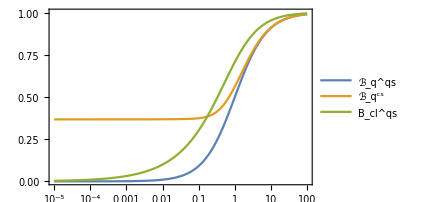

```mathematica
ListPlot[{{#1,2Abs[#2]}&@@@outset,{#1,2Abs[#3]}&@@@outset,{#1,#4//Re}&@@@outset},ScalingFunctions->{"Log",None},
PlotRange->{0.,1},
Joined->True,
PlotLegends->legend[{"ℬ_q^qs","ℬ_q^cs","B_cl^qs"},{0.3,0.7}]
]
```

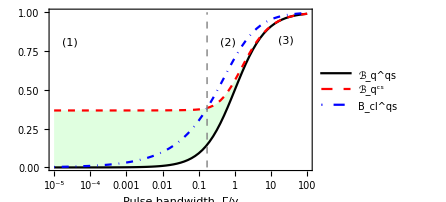

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16777136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
 |  |  |  |

```mathematica
Fig3=ListPlot[{{#1,2Abs[#2]}&@@@outset,{#1,2Abs[#3]}&@@@outset,{#1,#4//Re}&@@@outset},ScalingFunctions->{"Log",None},
PlotRange->{0.,1},
Joined->True,
PlotStyle->{Directive[Black],Directive[Dashed,Red],Directive[DotDashed,Blue]},
PlotLegends->legend[{"ℬ_q^qs","ℬ_q^cs","B_cl^qs"},{0.4,0.7}],
Epilog->{{Dashed,Gray,Line[{{Log10[0.017],0},{Log10[0.017],1}}]},Text["(1)",Scaled[{0.05,0.8}],{-1,0}],Text["(2)",Scaled[{0.68,0.8}]],,Text["(3)",Scaled[{0.9,0.81}]]},FrameLabel->{Style["Pulse bandwidth, Γ/γ",22,Black],None},
Filling->{1->{2}},
FillingStyle->LightGreen,
GridLines->{{Log10[0.017]},None},
GridLinesStyle->Directive[Dashed,LightRed]
]
savePlot["cBhat.pdf",%];
```